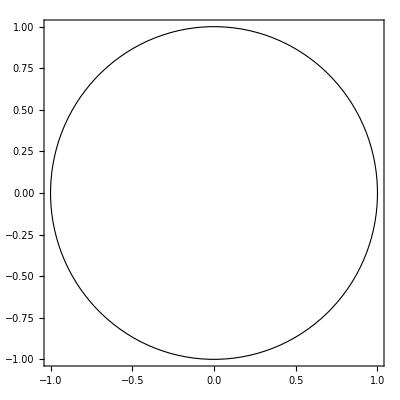

```mathematica
(*Define the Poincaré disk*)
disk = Disk[{0.0, 0.0},1];
(*Plot the Poincaré disk*)
Graphics[{EdgeForm[Black],White,disk},Frame->True,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Axes->True]
```

```mathematica
(*Define the Poincaré disk function*)
diskFunction=Evaluate[ImplicitRegion[x^2+y^2<1,{x,y}]];
```

```mathematica
f[theta_]:= r Cos[theta]
g[theta_] := r Sin[theta]
f'[theta]
f''[theta]
g'[theta]
g''[theta]
```

-r Sin[theta]

-r Cos[theta]

r Cos[theta]

-r Sin[theta]

```mathematica
ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Polar","Metric",{r,θ}],{r,θ},Kind->"Second"]
```

{{{0,0},{0,-r}},{{0,1/r},{1/r,0}}}

```mathematica
geo1[theta_] = f''[theta]+ 0 * f'[theta]^2+2 * 0 * f'[theta] * g'[theta]+ -r * g'[theta]^2
geo2[theta_]= g''[theta]+ 0* f'[theta]^2+ 2 *(1/r) * f'[theta]* g'[theta]+ 0 *g'[theta]^2
```

-r Cos[theta]-r^3 Cos[theta]^2

-r Sin[theta]-2 r Cos[theta] Sin[theta]

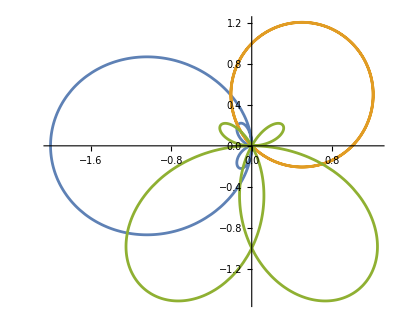

```mathematica
PolarPlot[{- Cos[theta] - (Cos[theta])^2, Cos[theta]+ Sin[theta], -Sin[theta]-2Cos[theta]Sin[theta]}, {theta, 0 , 2Pi}]
```